```mathematica
MyFolderX=NotebookDirectory[]
```

/Users/shawnliang/Desktop/Data & Code/Midterm/

```mathematica
(* Store filepath (string) of PersonData_ALL_N_354842_ALL.txt file in FilePathX *)
FilePathX=StringJoin[MyFolderX,"PersonData_ALL_N_354842_ALL.txt"]
```

/Users/shawnliang/Desktop/Data & Code/Midterm/PersonData_ALL_N_354842_ALL.txt

```mathematica
(* Import Data > Store in the local variabe "Din" *)
Din=Import[FilePathX,"CSV",CharacterEncoding-> "UTF8","TextDelimiters"->"\""];
```

```mathematica
NDataALL = Length[Din]
```

354842

```mathematica
1.Time Period Between 1920s and 1930s  --Men Occupation Types in the United States [ During World War II ]
```

```mathematica
HeaderX={"Name","FullName","Gender","NationalityCountries","BirthDate","DeathDate","BirthPlace","DeathPlace","Occupation","Wives","Husbands"};

(* Choose from Dataset to obtain 1890s-1900s indivduals, and cleaning the data by getting rid of NotAvailable data, and rounding the year to decades.*)
```

```mathematica
DinFirst = Reap[For[i = 1, i<NDataALL, i++,
If[(ToExpression[StringDrop[Din[[i]][[5]],-7]]*10 == 1930 || (ToExpression[StringDrop[Din[[i]][[5]],-7]]*10 ==1940)) &&
(Din[[i]][[4]]== "UnitedStates")&&
(Din[[i]][[3]]== "Male")&&
(Din[[i]][[-3]]!= "NotAvailable"), Sow[Din[[i]]]
]]][[2]][[1]];
DinFirst[[1;;3]]
Length[DinFirst]
```

{{A. C. Cowlings,Allen G. Cowlings,Male,UnitedStates,1947-06-16,NotAvailable,SanFrancisco;California;UnitedStates,NotAvailable,football player,NotAvailable,NotAvailable},{A.D. Whitfield,A.D. Whitfield,Male,UnitedStates,1943-09-02,NotAvailable,Rosebud;Texas;UnitedStates,NotAvailable,football player,NotAvailable,NotAvailable},{A.D. Williams,A.D. Williams,Male,UnitedStates,1933-11-21,NotAvailable,LittleRock;Arkansas;UnitedStates,NotAvailable,football player,NotAvailable,NotAvailable}}

15739

```mathematica
2. Count Different Birth Years and Occupation Types from People Dataset
```

```mathematica
DBirthYearFirst = DinFirst
DBirthYearFirst= Reap[For[i = 1, i <= Length[DBirthYearFirst], i++,
Sow[ToExpression[StringDrop[DBirthYearFirst[[i]][[5]],-7]]*10]]][[2]][[1]];
```

{{A. C. Cowlings,Allen G. Cowlings,Male,UnitedStates,1947-06-16,NotAvailable,SanFrancisco;California;UnitedStates,NotAvailable,football player,NotAvailable,NotAvailable},15737,{Steve "The Colonel" Cropper,Steve "The Colonel" Cropper,Male,UnitedStates,1941-10-21,NotAvailable,Missouri,NotAvailable,musician,Angel Cropper,NotAvailable}}
 |  |  |  |

```mathematica
(*The Amount of in this dataset *)
Length[DBirthYearFirst]
DBirthYearFirst[[1;;10]]
```

15739

{1940,1940,1930,1930,1940,1940,1930,1940,1930,1940}

```mathematica
DOccupationsFirst= DinFirst
DOccupationsFirst= Reap[For[i = 1, i <= Length[DOccupationsFirst], i++,
Sow[DOccupationsFirst[[i]][[-3]]]]][[2]][[1]];
```

{{A. C. Cowlings,Allen G. Cowlings,Male,UnitedStates,1947-06-16,NotAvailable,SanFrancisco;California;UnitedStates,NotAvailable,football player,NotAvailable,NotAvailable},15737,{Steve "The Colonel" Cropper,Steve "The Colonel" Cropper,Male,UnitedStates,1941-10-21,NotAvailable,Missouri,NotAvailable,musician,Angel Cropper,NotAvailable}}
 |  |  |  |

```mathematica
(* Combine Year and Occupation data sets,
sepereate the occupations for when an indidual has more than one *)
```

```mathematica
DOC = Transpose[{DBirthYearFirst,DOccupationsFirst}];
DOC[[1;;2]]

SplitDOC = Reap[For[i = 1,i≤Length[DOC],i++,
s = StringSplit[DOC[[i,2]],";"];

For[j = 1,j≤ Length[s],j++,
Sow[{DOC[[i,1]],s[[j]]}]
]

]][[2]][[1]];
```

{{1940,football player},{1940,football player}}

```mathematica
(* Tally the data and get the repeated times in dataset for years and occupations)
```

```mathematica
YDOC = Tally[Flatten[SplitDOC[[All,1]]]];
TableForm[YDOC]
```

1940 | 11615
1930 | 7671

```mathematica
3) Define Bipartite matrix associating people with their interests - use a sorted interest-index
```

```mathematica
(* Only take the first 200 data from the split data, because the larger the dataset, the messier the graphs.
This way we can have a more clear overall analysis.*)
NewDOC = SplitDOC[[1;;200]];
NewDOC[[-1]]
```

{1930,military}

```mathematica
NewODOC = Tally[Flatten[NewDOC[[All,2]]]];
TableForm[NewODOC]
Length[NewODOC]
(* Below are the first 200 occupations and number of times they appear in 1890s - 1900s *)
```

football player | 43
auto racer | 1
actor | 10
economist | 1
playwright | 1
novelist | 3
writer | 5
publisher | 2
journalist | 3
activist | 2
captain | 1
musician | 7
baseball player | 28
producer | 1
academy award winner | 1
businessperson | 11
politician | 11
songwriter | 2
columnist | 1
diplomat | 3
dancer | 1
designer | 2
academy award nominee | 5
author | 2
drummer | 3
singer | 1
fashion designer | 1
guitarist | 2
radio personality | 2
religious | 1
basketball player | 9
architect | 2
coach | 1
american football player | 1
physician | 1
singer/songwriter | 1
artist | 3
editor | 1
teacher | 1
photographer | 1
criminal | 1
astronomer | 1
historian | 1
attorney | 1
computer programmer | 1
conductor | 1
pianist | 2
mathematician | 1
entrepreneur | 1
educator | 1
professor | 1
military | 2
athlete | 3
commentator | 1
philanthropist | 1
composer | 1
tv personality | 1
association football player | 1

58

```mathematica
(* Create "dictionary" which maps a person/interest name to an index *)
Clear[MapYeari]
For[i=1,i≤Length[YDOC],i++,MapYeari[YDOC[[i,1]]]=i; ];
```

```mathematica
MapYeari[YDOC[[1,1]]]
MapYeari[YDOC[[-1,1]]]
```

1

2

```mathematica
Clear[MapOccupationj];
For[i=1,i≤Length[NewODOC],i++,MapOccupationj[NewODOC[[i]][[1]]]=i; ];
```

```mathematica
Length[NewODOC]
```

58

```mathematica
(* Calculate the bipartite association matrix *)
YearOccupationMatrix=Array[0&,{Length[YDOC],Length[NewODOC]}];
For[i=1,i≤Length[NewDOC],i++,
nInt=MapOccupationj[NewDOC[[i,2]]];
mInt=MapYeari[NewDOC[[i,1]]];
YearOccupationMatrix[[mInt]][[nInt]]=YearOccupationMatrix[[mInt]][[nInt]]+1;
];

MatrixForm[YearOccupationMatrix]
```

(25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
18 | 1 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 0)

```mathematica
Show[Colorize[YearOccupationMatrix],ImageSize-> 400,AspectRatio-> 1]
```

-Graphics-

```mathematica
4) Define Year-Year and Occupation-Occupation association matrix using bipartite projection method
```

```mathematica
(* Year-Year association matrix *)
YearYearBipartiteProj=YearOccupationMatrix.Transpose[YearOccupationMatrix];
Length[YearYearBipartiteProj]
For[i=1,i≤ Length[YearYearBipartiteProj],i++, YearYearBipartiteProj[[i]][[i]]=0;] 
(* Delete diagonal elements *)
MatrixForm[YearYearBipartiteProj] (* Number of occupations are the same in these years*)
```

2

(0 | 724
724 | 0)

```mathematica
(* Occupation-Occupation association matrix *)
OccupationOccupationBipartiteProj=Transpose[YearOccupationMatrix].YearOccupationMatrix;
Length[OccupationOccupationBipartiteProj]
For[i=1,i≤ Length[OccupationOccupationBipartiteProj],i++, OccupationOccupationBipartiteProj[[i]][[i]]=0;] 
(* Delete diagonal elements *)

(* Display Matrix of first 20 occupaton to occupation *)
MatrixForm[OccupationOccupationBipartiteProj]
```

58

(0 | 18 | 208 | 25 | 18 | 61 | 111 | 36 | 68 | 43 | 25 | 168 | 644 | 25 | 25 | 254 | 261 | 50 | 25 | 54 | 25 | 50 | 104 | 50 | 68 | 18 | 18 | 50 | 43 | 18 | 183 | 50 | 25 | 25 | 25 | 25 | 61 | 18 | 18 | 18 | 25 | 18 | 18 | 25 | 25 | 25 | 43 | 25 | 18 | 18 | 18 | 43 | 54 | 25 | 25 | 18 | 25 | 25
18 | 0 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 0
208 | 6 | 0 | 4 | 6 | 16 | 24 | 12 | 14 | 10 | 4 | 30 | 128 | 4 | 4 | 50 | 48 | 8 | 4 | 18 | 4 | 8 | 26 | 8 | 14 | 6 | 6 | 8 | 10 | 6 | 48 | 8 | 4 | 4 | 4 | 4 | 16 | 6 | 6 | 6 | 4 | 6 | 6 | 4 | 4 | 4 | 10 | 4 | 6 | 6 | 6 | 10 | 18 | 4 | 4 | 6 | 4 | 4
25 | 0 | 4 | 0 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
18 | 1 | 6 | 0 | 0 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 0
61 | 2 | 16 | 1 | 2 | 0 | 7 | 4 | 4 | 3 | 1 | 8 | 36 | 1 | 1 | 14 | 13 | 2 | 1 | 6 | 1 | 2 | 8 | 2 | 4 | 2 | 2 | 2 | 3 | 2 | 15 | 2 | 1 | 1 | 1 | 1 | 5 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 3 | 1 | 2 | 2 | 2 | 3 | 6 | 1 | 1 | 2 | 1 | 1
111 | 2 | 24 | 3 | 2 | 7 | 0 | 4 | 8 | 5 | 3 | 20 | 76 | 3 | 3 | 30 | 31 | 6 | 3 | 6 | 3 | 6 | 12 | 6 | 8 | 2 | 2 | 6 | 5 | 2 | 21 | 6 | 3 | 3 | 3 | 3 | 7 | 2 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 5 | 3 | 2 | 2 | 2 | 5 | 6 | 3 | 3 | 2 | 3 | 3
36 | 2 | 12 | 0 | 2 | 4 | 4 | 0 | 2 | 2 | 0 | 2 | 16 | 0 | 0 | 6 | 4 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 2 | 2 | 2 | 0 | 2 | 2 | 12 | 0 | 0 | 0 | 0 | 0 | 4 | 2 | 2 | 2 | 0 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 2 | 6 | 0 | 0 | 2 | 0 | 0
68 | 1 | 14 | 2 | 1 | 4 | 8 | 2 | 0 | 3 | 2 | 13 | 48 | 2 | 2 | 19 | 20 | 4 | 2 | 3 | 2 | 4 | 7 | 4 | 5 | 1 | 1 | 4 | 3 | 1 | 12 | 4 | 2 | 2 | 2 | 2 | 4 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 3 | 2 | 1 | 1 | 1 | 3 | 3 | 2 | 2 | 1 | 2 | 2
43 | 1 | 10 | 1 | 1 | 3 | 5 | 2 | 3 | 0 | 1 | 7 | 28 | 1 | 1 | 11 | 11 | 2 | 1 | 3 | 1 | 2 | 5 | 2 | 3 | 1 | 1 | 2 | 2 | 1 | 9 | 2 | 1 | 1 | 1 | 1 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 1 | 1 | 1 | 1 | 1
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 0 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
168 | 1 | 30 | 6 | 1 | 8 | 20 | 2 | 13 | 7 | 6 | 0 | 128 | 6 | 6 | 51 | 56 | 12 | 6 | 3 | 6 | 12 | 15 | 12 | 13 | 1 | 1 | 12 | 7 | 1 | 24 | 12 | 6 | 6 | 6 | 6 | 8 | 1 | 1 | 1 | 6 | 1 | 1 | 6 | 6 | 6 | 7 | 6 | 1 | 1 | 1 | 7 | 3 | 6 | 6 | 1 | 6 | 6
644 | 8 | 128 | 20 | 8 | 36 | 76 | 16 | 48 | 28 | 20 | 128 | 0 | 20 | 20 | 184 | 196 | 40 | 20 | 24 | 20 | 40 | 64 | 40 | 48 | 8 | 8 | 40 | 28 | 8 | 108 | 40 | 20 | 20 | 20 | 20 | 36 | 8 | 8 | 8 | 20 | 8 | 8 | 20 | 20 | 20 | 28 | 20 | 8 | 8 | 8 | 28 | 24 | 20 | 20 | 8 | 20 | 20
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 0 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 0 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
254 | 3 | 50 | 8 | 3 | 14 | 30 | 6 | 19 | 11 | 8 | 51 | 184 | 8 | 8 | 0 | 78 | 16 | 8 | 9 | 8 | 16 | 25 | 16 | 19 | 3 | 3 | 16 | 11 | 3 | 42 | 16 | 8 | 8 | 8 | 8 | 14 | 3 | 3 | 3 | 8 | 3 | 3 | 8 | 8 | 8 | 11 | 8 | 3 | 3 | 3 | 11 | 9 | 8 | 8 | 3 | 8 | 8
261 | 2 | 48 | 9 | 2 | 13 | 31 | 4 | 20 | 11 | 9 | 56 | 196 | 9 | 9 | 78 | 0 | 18 | 9 | 6 | 9 | 18 | 24 | 18 | 20 | 2 | 2 | 18 | 11 | 2 | 39 | 18 | 9 | 9 | 9 | 9 | 13 | 2 | 2 | 2 | 9 | 2 | 2 | 9 | 9 | 9 | 11 | 9 | 2 | 2 | 2 | 11 | 6 | 9 | 9 | 2 | 9 | 9
50 | 0 | 8 | 2 | 0 | 2 | 6 | 0 | 4 | 2 | 2 | 12 | 40 | 2 | 2 | 16 | 18 | 0 | 2 | 0 | 2 | 4 | 4 | 4 | 4 | 0 | 0 | 4 | 2 | 0 | 6 | 4 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 2 | 2
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 0 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
54 | 3 | 18 | 0 | 3 | 6 | 6 | 6 | 3 | 3 | 0 | 3 | 24 | 0 | 0 | 9 | 6 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 3 | 3 | 3 | 0 | 3 | 3 | 18 | 0 | 0 | 0 | 0 | 0 | 6 | 3 | 3 | 3 | 0 | 3 | 3 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 3 | 3 | 9 | 0 | 0 | 3 | 0 | 0
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
50 | 0 | 8 | 2 | 0 | 2 | 6 | 0 | 4 | 2 | 2 | 12 | 40 | 2 | 2 | 16 | 18 | 4 | 2 | 0 | 2 | 0 | 4 | 4 | 4 | 0 | 0 | 4 | 2 | 0 | 6 | 4 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 2 | 2
104 | 3 | 26 | 2 | 3 | 8 | 12 | 6 | 7 | 5 | 2 | 15 | 64 | 2 | 2 | 25 | 24 | 4 | 2 | 9 | 2 | 4 | 0 | 4 | 7 | 3 | 3 | 4 | 5 | 3 | 24 | 4 | 2 | 2 | 2 | 2 | 8 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 2 | 2 | 5 | 2 | 3 | 3 | 3 | 5 | 9 | 2 | 2 | 3 | 2 | 2
50 | 0 | 8 | 2 | 0 | 2 | 6 | 0 | 4 | 2 | 2 | 12 | 40 | 2 | 2 | 16 | 18 | 4 | 2 | 0 | 2 | 4 | 4 | 0 | 4 | 0 | 0 | 4 | 2 | 0 | 6 | 4 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 2 | 2
68 | 1 | 14 | 2 | 1 | 4 | 8 | 2 | 5 | 3 | 2 | 13 | 48 | 2 | 2 | 19 | 20 | 4 | 2 | 3 | 2 | 4 | 7 | 4 | 0 | 1 | 1 | 4 | 3 | 1 | 12 | 4 | 2 | 2 | 2 | 2 | 4 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 3 | 2 | 1 | 1 | 1 | 3 | 3 | 2 | 2 | 1 | 2 | 2
18 | 1 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 0
18 | 1 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 0
50 | 0 | 8 | 2 | 0 | 2 | 6 | 0 | 4 | 2 | 2 | 12 | 40 | 2 | 2 | 16 | 18 | 4 | 2 | 0 | 2 | 4 | 4 | 4 | 4 | 0 | 0 | 0 | 2 | 0 | 6 | 4 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 2 | 2
43 | 1 | 10 | 1 | 1 | 3 | 5 | 2 | 3 | 2 | 1 | 7 | 28 | 1 | 1 | 11 | 11 | 2 | 1 | 3 | 1 | 2 | 5 | 2 | 3 | 1 | 1 | 2 | 0 | 1 | 9 | 2 | 1 | 1 | 1 | 1 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 1 | 1 | 1 | 1 | 1
18 | 1 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 0
183 | 6 | 48 | 3 | 6 | 15 | 21 | 12 | 12 | 9 | 3 | 24 | 108 | 3 | 3 | 42 | 39 | 6 | 3 | 18 | 3 | 6 | 24 | 6 | 12 | 6 | 6 | 6 | 9 | 6 | 0 | 6 | 3 | 3 | 3 | 3 | 15 | 6 | 6 | 6 | 3 | 6 | 6 | 3 | 3 | 3 | 9 | 3 | 6 | 6 | 6 | 9 | 18 | 3 | 3 | 6 | 3 | 3
50 | 0 | 8 | 2 | 0 | 2 | 6 | 0 | 4 | 2 | 2 | 12 | 40 | 2 | 2 | 16 | 18 | 4 | 2 | 0 | 2 | 4 | 4 | 4 | 4 | 0 | 0 | 4 | 2 | 0 | 6 | 0 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 2 | 2
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
61 | 2 | 16 | 1 | 2 | 5 | 7 | 4 | 4 | 3 | 1 | 8 | 36 | 1 | 1 | 14 | 13 | 2 | 1 | 6 | 1 | 2 | 8 | 2 | 4 | 2 | 2 | 2 | 3 | 2 | 15 | 2 | 1 | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 3 | 1 | 2 | 2 | 2 | 3 | 6 | 1 | 1 | 2 | 1 | 1
18 | 1 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 0
18 | 1 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 0
18 | 1 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 0
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
18 | 1 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 0
18 | 1 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 0
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
43 | 1 | 10 | 1 | 1 | 3 | 5 | 2 | 3 | 2 | 1 | 7 | 28 | 1 | 1 | 11 | 11 | 2 | 1 | 3 | 1 | 2 | 5 | 2 | 3 | 1 | 1 | 2 | 2 | 1 | 9 | 2 | 1 | 1 | 1 | 1 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 2 | 3 | 1 | 1 | 1 | 1 | 1
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1
18 | 1 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 0
18 | 1 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 0
18 | 1 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 3 | 0 | 0 | 1 | 0 | 0
43 | 1 | 10 | 1 | 1 | 3 | 5 | 2 | 3 | 2 | 1 | 7 | 28 | 1 | 1 | 11 | 11 | 2 | 1 | 3 | 1 | 2 | 5 | 2 | 3 | 1 | 1 | 2 | 2 | 1 | 9 | 2 | 1 | 1 | 1 | 1 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 0 | 3 | 1 | 1 | 1 | 1 | 1
54 | 3 | 18 | 0 | 3 | 6 | 6 | 6 | 3 | 3 | 0 | 3 | 24 | 0 | 0 | 9 | 6 | 0 | 0 | 9 | 0 | 0 | 9 | 0 | 3 | 3 | 3 | 0 | 3 | 3 | 18 | 0 | 0 | 0 | 0 | 0 | 6 | 3 | 3 | 3 | 0 | 3 | 3 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 3 | 3 | 0 | 0 | 0 | 3 | 0 | 0
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1
18 | 1 | 6 | 0 | 1 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 8 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 3 | 0 | 0 | 0 | 0 | 0
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1
25 | 0 | 4 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 1 | 6 | 20 | 1 | 1 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0)

```mathematica
(* Degree Distribution *)
DegreeX=Total[Sign[#]]&/@OccupationOccupationBipartiteProj
```

{57,33,57,40,33,57,57,33,57,57,40,57,57,40,40,57,57,40,40,33,40,40,57,40,57,33,33,40,57,33,57,40,40,40,40,40,57,33,33,33,40,33,33,40,40,40,57,40,33,33,33,57,33,40,40,33,40,40}

```mathematica
5) WeightedAdjacencyGraph[ ]
```

```mathematica
mat=Replace[OccupationOccupationBipartiteProj,0->Infinity,{2}]; (*  0s represented by infinity in WeightedAdjacencyGraph[ ] *)
OName=NewODOC[[All,1]];

(* Set Labels : The "keys" for each node will be the name stored in OName *)
NameFontSizeX=20;
NodeColorX=Black;
LabelsetBlack=Table[OName[[i]]->Placed[ Style[OName[[i]],FontFamily->"Helvetica",NameFontSizeX,NodeColorX],Center],{i,Length[OName]}]
```

{football player→Placed[football player,Center],auto racer→Placed[auto racer,Center],actor→Placed[actor,Center],economist→Placed[economist,Center],playwright→Placed[playwright,Center],novelist→Placed[novelist,Center],writer→Placed[writer,Center],publisher→Placed[publisher,Center],journalist→Placed[journalist,Center],activist→Placed[activist,Center],captain→Placed[captain,Center],musician→Placed[musician,Center],baseball player→Placed[baseball player,Center],producer→Placed[producer,Center],academy award winner→Placed[academy award winner,Center],businessperson→Placed[businessperson,Center],politician→Placed[politician,Center],songwriter→Placed[songwriter,Center],columnist→Placed[columnist,Center],diplomat→Placed[diplomat,Center],dancer→Placed[dancer,Center],designer→Placed[designer,Center],academy award nominee→Placed[academy award nominee,Center],author→Placed[author,Center],drummer→Placed[drummer,Center],singer→Placed[singer,Center],fashion designer→Placed[fashion designer,Center],guitarist→Placed[guitarist,Center],radio personality→Placed[radio personality,Center],religious→Placed[religious,Center],basketball player→Placed[basketball player,Center],architect→Placed[architect,Center],coach→Placed[coach,Center],american football player→Placed[american football player,Center],physician→Placed[physician,Center],singer/songwriter→Placed[singer/songwriter,Center],artist→Placed[artist,Center],editor→Placed[editor,Center],teacher→Placed[teacher,Center],photographer→Placed[photographer,Center],criminal→Placed[criminal,Center],astronomer→Placed[astronomer,Center],historian→Placed[historian,Center],attorney→Placed[attorney,Center],computer programmer→Placed[computer programmer,Center],conductor→Placed[conductor,Center],pianist→Placed[pianist,Center],mathematician→Placed[mathematician,Center],entrepreneur→Placed[entrepreneur,Center],educator→Placed[educator,Center],professor→Placed[professor,Center],military→Placed[military,Center],athlete→Placed[athlete,Center],commentator→Placed[commentator,Center],philanthropist→Placed[philanthropist,Center],composer→Placed[composer,Center],tv personality→Placed[tv personality,Center],association football player→Placed[association football player,Center]}

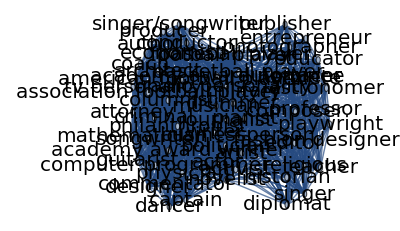

```mathematica
(* Plot Network - an ugly mess *)
g=WeightedAdjacencyGraph[OName,mat,VertexLabels->LabelsetBlack]
```

```mathematica
Clustering Coefficients - to what degree are neighbors connected?
```

```mathematica
(* Global - Network-level characteristic: What fraction of possible triangles (1st order cycle) exist in the network *)
N[GlobalClusteringCoefficient[g]]
```

0.873495

```mathematica
(* Local - Node-level characteristic: What fraction of possible triangles (1st order cycle) exist in the network *)LClusteringCoeffX=N[LocalClusteringCoefficient[g]]
Mean[LClusteringCoeffX]
N[MeanClusteringCoefficient[g]] (* Gives same result as above *)
```

{0.744361,1.,0.744361,1.,1.,0.744361,0.744361,1.,0.744361,0.744361,1.,0.744361,0.744361,1.,1.,0.744361,0.744361,1.,1.,1.,1.,1.,0.744361,1.,0.744361,1.,1.,1.,0.744361,1.,0.744361,1.,1.,1.,1.,1.,0.744361,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.744361,1.,1.,1.,1.,0.744361,1.,1.,1.,1.,1.,1.}

0.925071

0.925071

```mathematica
Length[LClusteringCoeffX]
```

58

```mathematica
Length[OName]
```

58

```mathematica
Sort[Thread[Rule[OName,LClusteringCoeffX]],#1[[2]]>#2[[2]]&]
```

{association football player→1.,tv personality→1.,composer→1.,philanthropist→1.,commentator→1.,athlete→1.,professor→1.,educator→1.,entrepreneur→1.,mathematician→1.,conductor→1.,computer programmer→1.,attorney→1.,historian→1.,astronomer→1.,criminal→1.,photographer→1.,teacher→1.,editor→1.,singer/songwriter→1.,physician→1.,american football player→1.,coach→1.,architect→1.,religious→1.,guitarist→1.,fashion designer→1.,singer→1.,author→1.,designer→1.,dancer→1.,diplomat→1.,columnist→1.,songwriter→1.,academy award winner→1.,producer→1.,captain→1.,publisher→1.,playwright→1.,economist→1.,auto racer→1.,military→0.744361,pianist→0.744361,artist→0.744361,basketball player→0.744361,radio personality→0.744361,drummer→0.744361,academy award nominee→0.744361,politician→0.744361,businessperson→0.744361,baseball player→0.744361,musician→0.744361,activist→0.744361,journalist→0.744361,writer→0.744361,novelist→0.744361,actor→0.744361,football player→0.744361}

{{57,0.744361},{33,1.},{57,0.744361},{40,1.},{33,1.},{57,0.744361},{57,0.744361},{33,1.},{57,0.744361},{57,0.744361},{40,1.},{57,0.744361},{57,0.744361},{40,1.},{40,1.},{57,0.744361},{57,0.744361},{40,1.},{40,1.},{33,1.},{40,1.},{40,1.},{57,0.744361},{40,1.},{57,0.744361},{33,1.},{33,1.},{40,1.},{57,0.744361},{33,1.},{57,0.744361},{40,1.},{40,1.},{40,1.},{40,1.},{40,1.},{57,0.744361},{33,1.},{33,1.},{33,1.},{40,1.},{33,1.},{33,1.},{40,1.},{40,1.},{40,1.},{57,0.744361},{40,1.},{33,1.},{33,1.},{33,1.},{57,0.744361},{33,1.},{40,1.},{40,1.},{33,1.},{40,1.},{40,1.}}

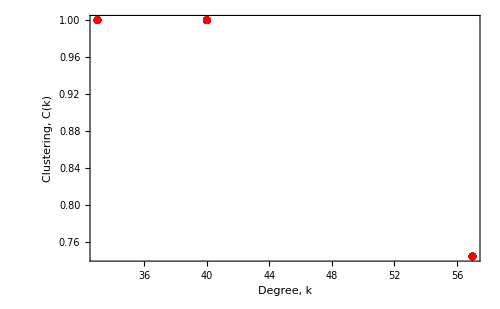

```mathematica
DegreeClusteringX=Thread[{DegreeX,LClusteringCoeffX}]

ListPlot[DegreeClusteringX,
PlotRange-> All,
PlotStyle->Directive[Red,10],
LabelStyle -> Directive[Black,FontSize->20,FontFamily-> "Helvetica"],
Frame->True,
ImageSize->{500,Automatic},
FrameLabel->{"Degree, k","Clustering, C(k)"},
ImageSize->500]
```

```mathematica
Improve network visualization layout
```

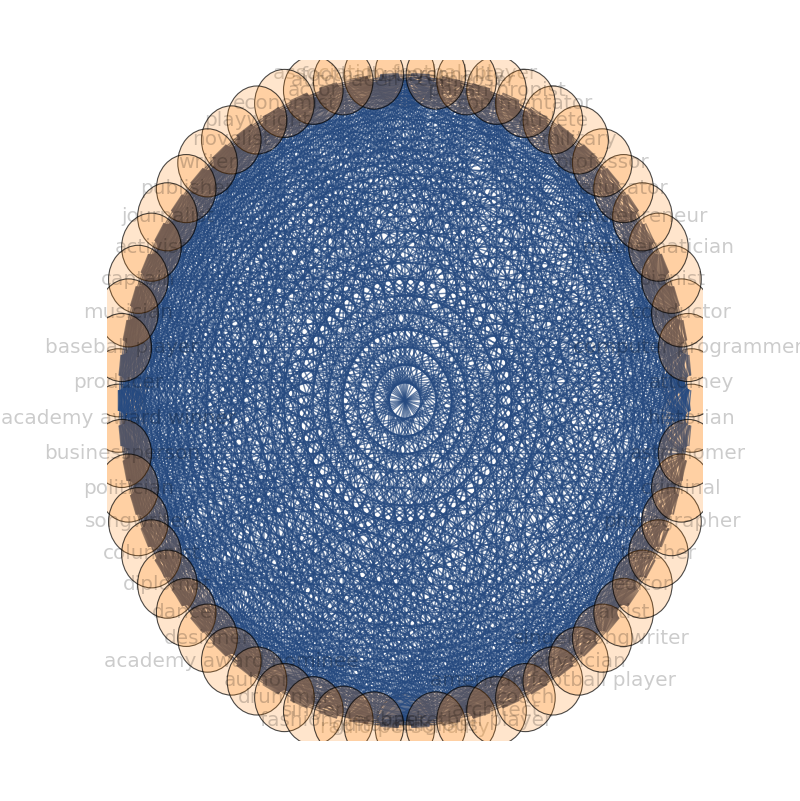

```mathematica
Circlesize=0.05;
r=Array[Circlesize&,Length[OName]]; (* Circle radius list *)

g=WeightedAdjacencyGraph[OName,mat,VertexLabels->LabelsetBlack,VertexSize->Scaled[.10],VertexStyle->Directive[Orange,Opacity[.2]],GraphLayout->{"CircularEmbedding"} ,ImageSize->800]
```

```mathematica
6) Modify the link color and thickness
```

```mathematica
(* AbsoluteOptions[ ]: gives the absolute settings of options specified in an expression such as a graphics object. *)
gEdWe=AbsoluteOptions[g,EdgeWeight][[All,2]][[1]]  (* Get list of edge weights associated with each edge *)
Max[gEdWe]
```

{18,208,25,18,61,111,36,68,43,25,168,644,25,25,254,261,50,25,54,25,50,104,50,68,18,18,50,43,18,183,50,25,25,25,25,61,18,18,18,25,18,18,25,25,25,43,25,18,18,18,43,54,25,25,18,25,25,6,1,2,2,2,1,1,1,8,3,2,3,3,1,1,1,1,1,6,2,1,1,1,1,1,1,1,1,1,1,3,1,4,6,16,24,12,14,10,4,30,128,4,4,50,48,8,4,18,4,8,26,8,14,6,6,8,10,6,48,8,4,4,4,4,16,6,6,6,4,6,6,4,4,4,10,4,6,6,6,10,18,4,4,6,4,4,1,3,2,1,1,6,20,1,1,8,9,2,1,1,2,2,2,2,2,1,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,8,3,2,3,3,1,1,1,1,1,6,2,1,1,1,1,1,1,1,1,1,1,3,1,7,4,4,3,1,8,36,1,1,14,13,2,1,6,1,2,8,2,4,2,2,2,3,2,15,2,1,1,1,1,5,2,2,2,1,2,2,1,1,1,3,1,2,2,2,3,6,1,1,2,1,1,4,8,5,3,20,76,3,3,30,31,6,3,6,3,6,12,6,8,2,2,6,5,2,21,6,3,3,3,3,7,2,2,2,3,2,2,3,3,3,5,3,2,2,2,5,6,3,3,2,3,3,2,2,2,16,6,4,6,6,2,2,2,2,2,12,4,2,2,2,2,2,2,2,2,2,2,6,2,3,2,13,48,2,2,19,20,4,2,3,2,4,7,4,5,1,1,4,3,1,12,4,2,2,2,2,4,1,1,1,2,1,1,2,2,2,3,2,1,1,1,3,3,2,2,1,2,2,1,7,28,1,1,11,11,2,1,3,1,2,5,2,3,1,1,2,2,1,9,2,1,1,1,1,3,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,3,1,1,1,1,1,6,20,1,1,8,9,2,1,1,2,2,2,2,2,1,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,128,6,6,51,56,12,6,3,6,12,15,12,13,1,1,12,7,1,24,12,6,6,6,6,8,1,1,1,6,1,1,6,6,6,7,6,1,1,1,7,3,6,6,1,6,6,20,20,184,196,40,20,24,20,40,64,40,48,8,8,40,28,8,108,40,20,20,20,20,36,8,8,8,20,8,8,20,20,20,28,20,8,8,8,28,24,20,20,8,20,20,1,8,9,2,1,1,2,2,2,2,2,1,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,9,2,1,1,2,2,2,2,2,1,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,78,16,8,9,8,16,25,16,19,3,3,16,11,3,42,16,8,8,8,8,14,3,3,3,8,3,3,8,8,8,11,8,3,3,3,11,9,8,8,3,8,8,18,9,6,9,18,24,18,20,2,2,18,11,2,39,18,9,9,9,9,13,2,2,2,9,2,2,9,9,9,11,9,2,2,2,11,6,9,9,2,9,9,2,2,4,4,4,4,4,2,6,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,1,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,9,3,3,3,3,3,18,6,3,3,3,3,3,3,3,3,3,3,9,3,2,2,2,2,2,1,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,4,4,4,2,6,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,7,3,3,4,5,3,24,4,2,2,2,2,8,3,3,3,2,3,3,2,2,2,5,2,3,3,3,5,9,2,2,3,2,2,4,4,2,6,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,4,3,1,12,4,2,2,2,2,4,1,1,1,2,1,1,2,2,2,3,2,1,1,1,3,3,2,2,1,2,2,1,1,1,6,2,1,1,1,1,1,1,1,1,1,1,3,1,1,1,6,2,1,1,1,1,1,1,1,1,1,1,3,1,2,6,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,9,2,1,1,1,1,3,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,3,1,1,1,1,1,6,2,1,1,1,1,1,1,1,1,1,1,3,1,6,3,3,3,3,15,6,6,6,3,6,6,3,3,3,9,3,6,6,6,9,18,3,3,6,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,2,2,1,1,1,3,1,2,2,2,3,6,1,1,2,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,3,1,1,3,1,3,1,1,1,1,1,3,1,1,1,1,1,1}

644

```mathematica
(* Use linear transform to rescale edge weight values to be from 0 to 1 *)
gEdWe=Rescale[gEdWe,{0,Max[gEdWe]},{0,1}]
```

{9/322,52/161,25/644,9/322,61/644,111/644,9/161,17/161,43/644,25/644,6/23,1,25/644,25/644,127/322,261/644,25/322,25/644,27/322,25/644,25/322,26/161,25/322,17/161,9/322,9/322,25/322,43/644,9/322,183/644,25/322,25/644,25/644,25/644,25/644,61/644,9/322,9/322,9/322,25/644,9/322,9/322,25/644,25/644,25/644,43/644,25/644,9/322,9/322,9/322,43/644,27/322,25/644,25/644,9/322,25/644,25/644,3/322,1/644,1/322,1/322,1/322,1/644,1/644,1/644,2/161,3/644,1/322,3/644,3/644,1/644,1/644,1/644,1/644,1/644,3/322,1/322,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,3/644,1/644,1/161,3/322,4/161,6/161,3/161,1/46,5/322,1/161,15/322,32/161,1/161,1/161,25/322,12/161,2/161,1/161,9/322,1/161,2/161,13/322,2/161,1/46,3/322,3/322,2/161,5/322,3/322,12/161,2/161,1/161,1/161,1/161,1/161,4/161,3/322,3/322,3/322,1/161,3/322,3/322,1/161,1/161,1/161,5/322,1/161,3/322,3/322,3/322,5/322,9/322,1/161,1/161,3/322,1/161,1/161,1/644,3/644,1/322,1/644,1/644,3/322,5/161,1/644,1/644,2/161,9/644,1/322,1/644,1/644,1/322,1/322,1/322,1/322,1/322,1/644,3/644,1/322,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/322,1/322,1/322,1/644,1/644,1/644,2/161,3/644,1/322,3/644,3/644,1/644,1/644,1/644,1/644,1/644,3/322,1/322,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,3/644,1/644,1/92,1/161,1/161,3/644,1/644,2/161,9/161,1/644,1/644,1/46,13/644,1/322,1/644,3/322,1/644,1/322,2/161,1/322,1/161,1/322,1/322,1/322,3/644,1/322,15/644,1/322,1/644,1/644,1/644,1/644,5/644,1/322,1/322,1/322,1/644,1/322,1/322,1/644,1/644,1/644,3/644,1/644,1/322,1/322,1/322,3/644,3/322,1/644,1/644,1/322,1/644,1/644,1/161,2/161,5/644,3/644,5/161,19/161,3/644,3/644,15/322,31/644,3/322,3/644,3/322,3/644,3/322,3/161,3/322,2/161,1/322,1/322,3/322,5/644,1/322,3/92,3/322,3/644,3/644,3/644,3/644,1/92,1/322,1/322,1/322,3/644,1/322,1/322,3/644,3/644,3/644,5/644,3/644,1/322,1/322,1/322,5/644,3/322,3/644,3/644,1/322,3/644,3/644,1/322,1/322,1/322,4/161,3/322,1/161,3/322,3/322,1/322,1/322,1/322,1/322,1/322,3/161,1/161,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,3/322,1/322,3/644,1/322,13/644,12/161,1/322,1/322,19/644,5/161,1/161,1/322,3/644,1/322,1/161,1/92,1/161,5/644,1/644,1/644,1/161,3/644,1/644,3/161,1/161,1/322,1/322,1/322,1/322,1/161,1/644,1/644,1/644,1/322,1/644,1/644,1/322,1/322,1/322,3/644,1/322,1/644,1/644,1/644,3/644,3/644,1/322,1/322,1/644,1/322,1/322,1/644,1/92,1/23,1/644,1/644,11/644,11/644,1/322,1/644,3/644,1/644,1/322,5/644,1/322,3/644,1/644,1/644,1/322,1/322,1/644,9/644,1/322,1/644,1/644,1/644,1/644,3/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/322,1/644,1/644,1/644,1/644,1/322,3/644,1/644,1/644,1/644,1/644,1/644,3/322,5/161,1/644,1/644,2/161,9/644,1/322,1/644,1/644,1/322,1/322,1/322,1/322,1/322,1/644,3/644,1/322,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,32/161,3/322,3/322,51/644,2/23,3/161,3/322,3/644,3/322,3/161,15/644,3/161,13/644,1/644,1/644,3/161,1/92,1/644,6/161,3/161,3/322,3/322,3/322,3/322,2/161,1/644,1/644,1/644,3/322,1/644,1/644,3/322,3/322,3/322,1/92,3/322,1/644,1/644,1/644,1/92,3/644,3/322,3/322,1/644,3/322,3/322,5/161,5/161,2/7,7/23,10/161,5/161,6/161,5/161,10/161,16/161,10/161,12/161,2/161,2/161,10/161,1/23,2/161,27/161,10/161,5/161,5/161,5/161,5/161,9/161,2/161,2/161,2/161,5/161,2/161,2/161,5/161,5/161,5/161,1/23,5/161,2/161,2/161,2/161,1/23,6/161,5/161,5/161,2/161,5/161,5/161,1/644,2/161,9/644,1/322,1/644,1/644,1/322,1/322,1/322,1/322,1/322,1/644,3/644,1/322,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,2/161,9/644,1/322,1/644,1/644,1/322,1/322,1/322,1/322,1/322,1/644,3/644,1/322,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,39/322,4/161,2/161,9/644,2/161,4/161,25/644,4/161,19/644,3/644,3/644,4/161,11/644,3/644,3/46,4/161,2/161,2/161,2/161,2/161,1/46,3/644,3/644,3/644,2/161,3/644,3/644,2/161,2/161,2/161,11/644,2/161,3/644,3/644,3/644,11/644,9/644,2/161,2/161,3/644,2/161,2/161,9/322,9/644,3/322,9/644,9/322,6/161,9/322,5/161,1/322,1/322,9/322,11/644,1/322,39/644,9/322,9/644,9/644,9/644,9/644,13/644,1/322,1/322,1/322,9/644,1/322,1/322,9/644,9/644,9/644,11/644,9/644,1/322,1/322,1/322,11/644,3/322,9/644,9/644,1/322,9/644,9/644,1/322,1/322,1/161,1/161,1/161,1/161,1/161,1/322,3/322,1/161,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/644,1/322,1/322,1/322,1/322,1/322,1/644,3/644,1/322,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,9/644,3/644,3/644,3/644,3/644,3/644,9/322,3/322,3/644,3/644,3/644,3/644,3/644,3/644,3/644,3/644,3/644,3/644,9/644,3/644,1/322,1/322,1/322,1/322,1/322,1/644,3/644,1/322,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/161,1/161,1/161,1/161,1/322,3/322,1/161,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/161,1/92,3/644,3/644,1/161,5/644,3/644,6/161,1/161,1/322,1/322,1/322,1/322,2/161,3/644,3/644,3/644,1/322,3/644,3/644,1/322,1/322,1/322,5/644,1/322,3/644,3/644,3/644,5/644,9/644,1/322,1/322,3/644,1/322,1/322,1/161,1/161,1/322,3/322,1/161,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/644,1/644,1/161,3/644,1/644,3/161,1/161,1/322,1/322,1/322,1/322,1/161,1/644,1/644,1/644,1/322,1/644,1/644,1/322,1/322,1/322,3/644,1/322,1/644,1/644,1/644,3/644,3/644,1/322,1/322,1/644,1/322,1/322,1/644,1/644,1/644,3/322,1/322,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,3/644,1/644,1/644,1/644,3/322,1/322,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,3/644,1/644,1/322,3/322,1/161,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/644,9/644,1/322,1/644,1/644,1/644,1/644,3/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/322,1/644,1/644,1/644,1/644,1/322,3/644,1/644,1/644,1/644,1/644,1/644,3/322,1/322,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,3/644,1/644,3/322,3/644,3/644,3/644,3/644,15/644,3/322,3/322,3/322,3/644,3/322,3/322,3/644,3/644,3/644,9/644,3/644,3/322,3/322,3/322,9/644,9/322,3/644,3/644,3/322,3/644,3/644,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/322,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/322,1/322,1/322,1/644,1/322,1/322,1/644,1/644,1/644,3/644,1/644,1/322,1/322,1/322,3/644,3/322,1/644,1/644,1/322,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,3/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,3/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,3/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,3/644,1/644,1/644,1/644,1/644,1/644,1/644,3/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/322,3/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,1/644,3/644,1/644,1/644,1/644,3/644,1/644,1/644,3/644,1/644,3/644,1/644,1/644,1/644,1/644,1/644,3/644,1/644,1/644,1/644,1/644,1/644,1/644}

```mathematica
(* Adjust the link properties *)
ThicknessBoost=8;
OpacityFactor=1; (* 1.15, 1, 1.1*)
RedGreenFactor=-1; (* 1 = Green, -1 = Red *)

(* Thread together the links with their modified color, opacity, and thickness values defined by gEdWe *)
(* The &/@gEdWe means that everywhere that there is a # in the Thread function it will use the corresponding list element in gEdWe *)
ModifiedEdgePropertiesX=
Thread[Rule[EdgeList[g],Directive[ColorData["RedGreenSplit"][Rescale[#,{-1*RedGreenFactor,1 *RedGreenFactor}]],Opacity[(OpacityFactor*#)],AbsoluteThickness[ThicknessBoost*#]]&/@gEdWe]];
Take[ModifiedEdgePropertiesX,3]
```

{football player<->auto racer→Directive[RGBColor[1., 0.9738387329192546, 0.9738387329192546],Opacity[9/322],AbsoluteThickness[36/161]],football player<->actor→Directive[RGBColor[1., 0.6976920248447205, 0.6976920248447205],Opacity[52/161],AbsoluteThickness[416/161]],football player<->economist→Directive[RGBColor[1., 0.9636649068322982, 0.9636649068322982],Opacity[25/644],AbsoluteThickness[50/161]]}

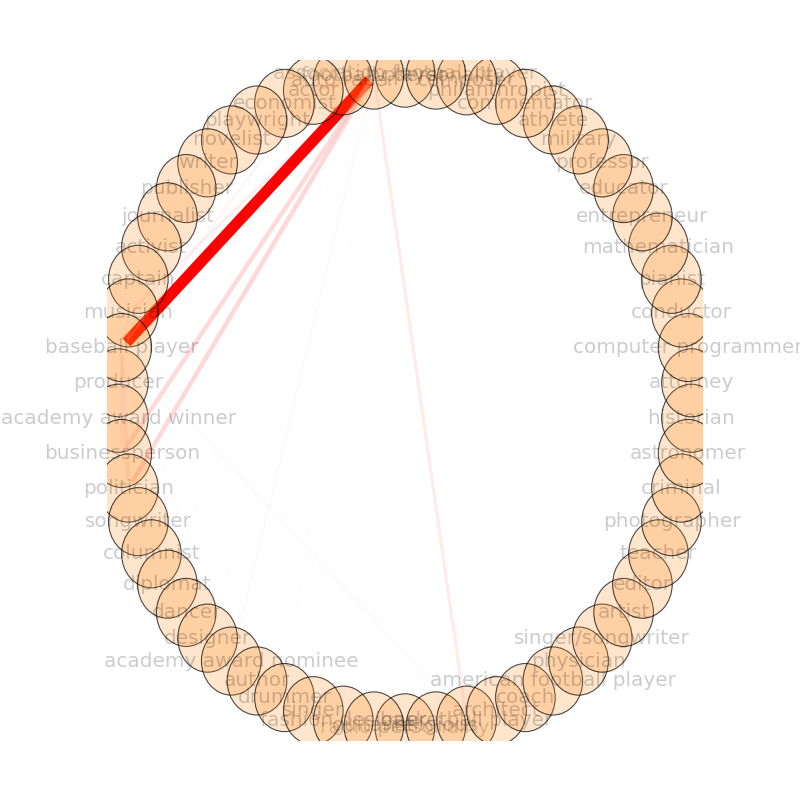

```mathematica
(* Adjust just one option stored in the graph g *)
g=SetProperty[g,EdgeStyle->ModifiedEdgePropertiesX];

Gfin=Show[g,ImagePadding->{{100,100},{100,100}}]
```